145.165

121.25

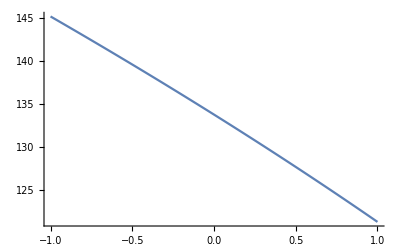

```mathematica
mA=97;
mB=144;
mC=180;
mXsq[x_]:=mA^2+((mC^2-mB^2)/(2mB^2))*(mB^2*(1-x)+mA^2*(1+x))
N[Sqrt[mXsq[-1]]]
N[Sqrt[mXsq[1]]]
Plot[Sqrt[mXsq[x]],{x,-1,1}]
```

```mathematica
mXlow=Sqrt[mXsq[1]];
mXhigh=Sqrt[mXsq[-1]];
```

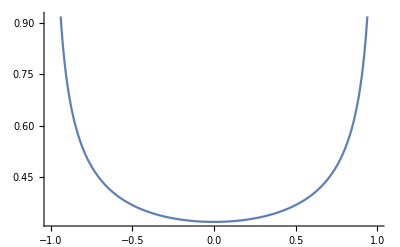

```mathematica
Plot[1/(Pi*Sqrt[1-y^2]),{y,-1,1}]
```

TransformedDistribution[√(9409+9/32 (20736 (1-y)+9409 (1+y))),y\[Distributed]ProbabilityDistribution[1/(√(1-x^2) π),{x,-1,1}]]

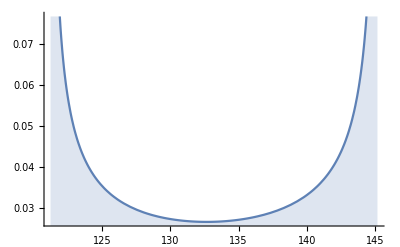

```mathematica
blah=TransformedDistribution[Sqrt[mXsq[y]],y\[Distributed]ProbabilityDistribution[1/(Pi*Sqrt[1-x^2]),{x,-1,1}]]
Plot[PDF[blah,x],{x,mXlow,mXhigh},Filling->Axis]
```

```mathematica
N[Integrate[PDF[blah,x],{x,mXhigh-5,mXhigh}]]
N[Integrate[PDF[blah,x],{x,mXlow,mXlow+5}]]
N[Integrate[PDF[blah,x],{x,mXlow,mXhigh}]]
```

0.313799

0.290547

1.